```mathematica
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["EnergyLoss`",NotebookDirectory[]<>"../packages/EnergyLoss.wl"]
```

## Load

### Scanning Parameters

#### masses

```mathematica
mpDPoints = Table["mpD"->10^i 10^9("JpereV")/("c")^2/.SIConstRepl,{i,-1,3}];(*We will scan from 10^-1 GeV to a TeV in increments of 10*)
```

```mathematica
meDPoints = Table["meD/mpD"->10^i,{i,-4,-2,2}];(*For each value of mpD we will scan over meD/mpD of 10^-4 and 10^-2*)
```

#### v0

```mathematica
v0Points = {20,220}10^3 ;(*[ms^-1] - average velocity of local aDM for Halo and Disk cases*)
```

### Load fit parameters and constants for each material

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

Need to include the band gap for the silicates

```mathematica
SiO2Totalparams=Table[ReplaceParams[SiO2Totalparams[[i]],8.90("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[SiO2Totalparams]}];
MgOTotalparams=Table[ReplaceParams[MgOTotalparams[[i]],7.77("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[MgOTotalparams]}];
```

### For Δr

#### Read EL dicts

Nuclear

```mathematica
FeNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/FeNuc0ELOutputDict"];
MgNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/MgNuc0ELOutputDict"];
SiNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/SiNuc0ELOutputDict"];
ONuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/ONuc0ELOutputDict"];
```

Electronic

```mathematica
FeeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/FeELOutputDictSIEnhanced"];
SiO2eELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/SiO2ELOutputDictSIEnhanced"];
MgOeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/MgOELOutputDictSIEnhanced"];
```

### Electronic dσ/dE_R Interpolation Tables

#### 0.1 GeV

```mathematica
FeσDictemep1GeV=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[1]],FeTotalparams[[i]],10,60,10^-4,4,True,True],{i,Length[FeTotalparams]}]
SaveIt[NotebookDirectory[]<>"FeσDicteme",FeσDictemep1GeV]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00114}. NIntegrate obtained 0.0021995 and 2.63835×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00129}. NIntegrate obtained 0.00219805 and 2.35504×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00166}. NIntegrate obtained 0.00219441 and 2.71769×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-734.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-853.697] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-992.694] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dσ interpolation done

σ interpolation done

dσ interpolation done

σ interpolation done

dσ interpolation done

σ interpolation done

dσ interpolation done

σ interpolation done

dσ interpolation done

σ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDicteme.dat

```mathematica
SiO2σDictemep1GeV=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[1]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True],{i,Length[SiO2Totalparams]}];
SaveIt[NotebookDirectory[]<>"SiO2σDicteme1GeV",SiO2σDictemep1GeV]
```

General::munfl: Exp[-737.656] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.975] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01823777020335885790114360816005500964820384979248046875}. NIntegrate obtained 0.00442715 and 9.4584×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01833237976527897494793961641335044987499713897705078125}. NIntegrate obtained 0.00442371 and 8.19232×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01844268722325083376123444622862734831869602203369140625}. NIntegrate obtained 0.00441968 and 5.60551×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-758.202] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dσ interpolation done

σ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDicteme1GeV.dat

```mathematica
MgOσDictemep1GeV=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[1]],MgOTotalparams[[i]],10,60,10^-4,4,True,True],{i,Length[MgOTotalparams]}];
SaveIt[NotebookDirectory[]<>"MgOσDictmep1GeV",MgOσDictemep1GeV]
```

General::munfl: Exp[-726.704] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-795.706] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-876.157] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.033535219968079676977623648781445808708667755126953125}. NIntegrate obtained 0.0034105 and 6.67258×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.03376852772614136188877864697133190929889678955078125}. NIntegrate obtained 0.00340698 and 6.73205×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.034040546591827369748983755926019512116909027099609375}. NIntegrate obtained 0.00340289 and 6.78681×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dσ interpolation done

σ interpolation done

dσ interpolation done

σ interpolation done

dσ interpolation done

σ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictmep1GeV.dat

### Nuclear dσ/dE_R Interpolation Tables

#### 0.1 GeV

```mathematica
FeσDictNucmep1GeV=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],FeNucCoeffs]
```

General::munfl: Exp[-19880.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3970.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1231.19] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
(*FeσDictNucmp1GeV=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],FeNucCoeffs,SIConstRepl,{4 10^-7,2 10^-1}"c"/.SIConstRepl,FeNucCoeffs,200,200,10^-4,False];*)
```

```mathematica
SiσDictNucmep1GeV=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],SiNucCoeffs]
```

General::munfl: Exp[-21044.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8329.39] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24536.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
MgσDictNucmep1GeV=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],MgNucCoeffs];
```

General::munfl: Exp[-20392.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1850.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-727.459] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
OσDictNucmep1GeV=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],ONucCoeffs];
```

General::munfl: Exp[-8429.26] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3400.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1460.28] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNucmep1GeV",FeσDictNucmep1GeV]
SaveIt[NotebookDirectory[]<>"SiσDictNucmep1GeV",SiσDictNucmep1GeV]
SaveIt[NotebookDirectory[]<>"MgσDictNucmep1GeV",MgσDictNucmep1GeV]
SaveIt[NotebookDirectory[]<>"OσDictNucmep1GeV",OσDictNucmep1GeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNucmep1GeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNucmep1GeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNucmep1GeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNucmep1GeV.dat

## Definitions

### Utilities

#### Convert from v0 to βD

```mathematica
Clear[v0toβD]
v0toβD[v0_,meD_,mpD_]:=Module[{βD,v0pD,v0eD},
(*
v0 is the average velocity of the aDM particles. By equipartition: v0 = 1/Subscript[N, χ] Subscript[Σ, χ] √(3/(Subscript[m, χ] βD)) = 1/2 √((3(Subscript[m, Subscript[e, D]] + Subscript[m, Subscript[p, D]]))/(βD Subscript[m, Subscript[e, D]] Subscript[m, Subscript[p, D]])) 
*)
βD = 3/(4 v0^2)(meD + mpD)/(meD mpD) ;
v0pD = √(3/(mpD βD));
v0eD = √(3/(meD βD)); 
<|"βD"->βD,"v0"->v0,"v0pD"->v0pD,"v0eD"->v0eD|>
]
```

```mathematica
Solve[βD == 1/(4v0ts)(3 (meD + mpD))/(meD mpD),v0ts][[1]]
(v0ts/.%)()
```

{v0ts→(3 (meD+mpD))/(4 meD mpD βD)}

(3 (meD+mpD))/(4 meD mpD βD)

### MC Processes

#### Gravitational Potential

```mathematica
Vgrav[r_]:=Piecewise[{{-(("G" "ME")/r),r>"rE"/. Constants`EarthRepl},{-(("ME" "G")/(2("rE")^3))( 3("rE")^2-r^2),r<"rE"/. Constants`EarthRepl}},-(("G" "ME")/("rE"/. Constants`EarthRepl))]/.Constants`SIConstRepl/.Constants`EarthRepl
```

#### Select Interaction Process

```mathematica
σselector[σs_]:=Module[{ξ2,Ps,Psums,Nσ,n},

ξ2 = Random[];

Nσ=Length[σs];
Ps=σs/Total[σs];
Psums=Table[Sum[Ps[[i]],{i,j}],{j,Length[Ps]}];

n=0;
Do[If[ ξ2<=Psums[[i]],n=i;Break[]],{i,1,Nσ}];
(*{n,ξ2,N[Psums]}*)
n
]
```

#### Region handling

```mathematica
CrustOrCore[r_]:=Piecewise[{{1,("rcore"/.Constants`EarthRepl)<r<=("rE"/.Constants`EarthRepl)},{2,r<("rcore"/.Constants`EarthRepl)}},3](*1 => in the crust, 2 => in the core, 3 => not in the Earth*)
```

```mathematica
SortProcessesByRegion[associationlist_,key_]:=Module[{sortedlist},
sortedlist={{},{},{}}; (*1 corresponds to crust, 2 to core, 3 to outside earth (empty)*)
Do[AppendTo[sortedlist[[("region"/.associationlist[[i]])]],key/.associationlist[[i]]],{i,Length[associationlist]}];
sortedlist
]
```

#### Δr total

```mathematica
Clear[ELEarthTot]

fTot0ELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(10^SiO2eELDict[["f"]][mχ,vχ]+10^SiNuc0ELDict[["f"]][mχ,vχ]+2 10^ONuc0ELDict[["f"]][mχ,vχ])+"MgOFrac"(10^MgOeELDict[["f"]] [mχ,vχ]+10^MgNuc0ELDict[["f"]][mχ,vχ]+ 10^ONuc0ELDict[["f"]][mχ,vχ])]/.EarthRepl
feELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(("ρM")/("ρSiO2")/.MassDensities)(10^SiO2eELDict[["f"]][mχ,vχ])+"MgOFrac"(("ρM")/("ρMgO")/.MassDensities)(10^MgOeELDict[["f"]] [mχ,vχ])]/.EarthRepl (*ignores slight change in densities from surface to mantle in densities (we showed it's irrelevant for iron in the core, so it will be even less significant here)*)
fTot0ELCore[mχ_,vχ_]:=Log10[10^FeeELDict[["f"]][mχ,vχ] + 10^FeNuc0ELDict[["f"]][mχ,vχ]]

 ELEarthTot[r_,mχ_,vχ_]:=Piecewise[{{10^fTot0ELMantle[Log10[mχ], Log10[vχ]],("rE"/.Constants`EarthRepl)> r >=  ("rcore"/.Constants`EarthRepl)},{10^fTot0ELCore[Log10[mχ], Log10[vχ]], ("rcore"/.Constants`EarthRepl)>r}},0]
```

```mathematica
dc[bE_] := 2 √(("rcore")^2-bE^2)/.Constants`EarthRepl (*path length in the core for given impact parameter*)
dE[bE_] := 2 √(("rE")^2-bE^2)/.Constants`EarthRepl (*path length through the earth*)
dM[bE_]:= If[(("rcore")^2/.Constants`EarthRepl)>bE^2,dE[bE] - dc[bE],Re[dE[bE]]](*path length through the Mantle, iff condition is satisfied does it go through the core*)
```

```mathematica
Clear[ΔrAveragedTot0,ΔETot0]

ΔETot0[mχ_,vχ_,κ_,bE_,consts_] :=Re[If[(("rcore")^2/.Constants`EarthRepl)>bE^2,(κ^2 "JpereV"(dM[bE] 10^fTot0ELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^fTot0ELCore[Log10[mχ], Log10[vχ]])) /.consts,(κ^2 "JpereV"(dM[bE] 10^fTot0ELMantle[Log10[mχ], Log10[vχ]])) /.consts ]](*assumes 0 temp nuclear*)
EK[mχ_,vχ_] :=1/2 mχ vχ^2
EKbyΔETot0[mχ_,vχ_,κ_,bE_,consts_] := EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]
ΔrAveragedTot0[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl,y_:10^-2]:= dE[bE] y EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]

fΔrAveragedTot0[mχ_,vχ_]:=Log10[ΔrAveragedTot0[10^mχ,10^vχ,1,10^-2,0,SIConstRepl]^-1]
```

**** should put this into a single module for Δr

#### Weak Capture Regime Trajectory

```mathematica
Clear[GetWeakCaptureTrajectory]
GetWeakCaptureTrajectory[mχ_,vχE_,bE_,κ_]:=Module[{RE,lsol,ldom,voft},
RE = dE[bE];(*path length through the Earth*)
lsol=l/.NDSolve[{D[l[t],{t,2}]==-(κ^2("JpereV"/.Constants`SIConstRepl))/mχ ELEarthTot[√(bE^2+l[t]^2),mχ,l'[t]],l'[0]==vχE,l[0]==-RE/2,WhenEvent[l[t]==RE/2,"StopIntegration"]},l,{t,0,10^4}][[1]];(*Solution for trajectory of particle along a straight line through the earth parallel to it's velocity as a function of time.*)
ldom=lsol["Domain"][[1]];
voft=lsol';
<|"l(t)"->lsol,"v(t)"->voft,"domain"->ldom,"RE"->RE,"κ"->κ,"bE"->bE,"mχ"->mχ|>
]
```

#### Weak Capture Regime Capture Probability

```mathematica
Clear[GetWeakCaptureProbability]
GetWeakCaptureProbability[lDict_,σDict_]:= Module[{vχmin,vχraw,vχ,mχ,ωmin,params,tdom,ωcapture,δξ,ξofωandt,ωmaxoft,dσdERoftandω,σoft,integralofλinvwrtr,SurvivalProb,CaptureProb},
ωmin="ωmin"/.σDict;
params=σDict["params"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.lDict);
tdom = "domain"/.lDict;

vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; (*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
vχraw=("v(t)"/.lDict);
vχ=If[vχraw[#]>vχmin,("v(t)"/.lDict)[#],0]&;

ξofωandt=Abs[EnergyLoss`ξofωandvχ[#1,ωmin,("v(t)"/.lDict)[#2],mχ,params]-δξ]&;
ωmaxoft=EnergyLoss`ωmaxofvχ[("v(t)"/.lDict)[#1],mχ,params]&;

dσdERoftandω=10^Re@("dσf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]&;

(*
(*Pre ωcapture*)
σoft=If[vχraw[#]>vχmin,("κ"/.lDict)^2("ne"/.params)NIntegrate[ dσdERoftandω[#,ω]("ℏ"/.params),{ω,ωmin,ωmaxoft[#]}],0]&;(* ℏ from the jacobians Subscript[E, R]->ω *)
*)

(*Post ωcapture*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (vχ[#]^2 - ("vesc"/.Constants`EarthRepl))&;
σoft=If[vχraw[#]>vχmin && ωmaxoft[#]>ωcapture[#],("κ"/.lDict)^2("ne"/.params)NIntegrate[ dσdERoftandω[#,ω]("ℏ"/.params),{ω,ωcapture[#],ωmaxoft[#]}],0]&;(* ℏ from the jacobians Subscript[E, R]->ω *)


integralofλinvwrtr=Total@Table[σoft[t]vχ[t],{t,Round[tdom[[1]]],Round[tdom[[2]]],1}];
(* vχ from the jacobians l -> t - do simple numerical integral here, Nintegrate was giving some weird divergin issues*)
SurvivalProb =E^-integralofλinvwrtr;
CaptureProb=1-SurvivalProb;

(*Print["Starting Nintegrate"];
Print@NIntegrate[σoft[t]vχ[t],{t,tdom[[1]],tdom[[2]]}];*)

<|"SurvivalProb"->SurvivalProb,"CaptureProb"->CaptureProb|>
]
```

-Graphics-

We run into this issue when we try to use NIntegrate for the survival probability integral

### Initial Conditions

```mathematica
Clear[Getvχ∞]
Getvχ∞[mχ_,βD_,maxrat_:Sqrt[20]]:=Module[{fMB,NMax,vχMax,vχMP,nits=0,vχ,P,Mξ,Accepted=False},
vχMP=Sqrt[2/(mχ βD)];(*most probable velocity in MB*)
vχMax = maxrat vχMP; (*maximum a simple rescaling of most probable, since higher velocities are exponentially suppressed*)
fMB=(#^2 E^(-βD mχ/2 #^2))&;
NMax=2/(E mχ βD);(*value of fMB at vχ MP*)
While[!Accepted && nits<30,
nits+=1;
vχ=Random[] vχMax;
(*Print[vχ];*)
Mξ=Random[]NMax;
P=fMB[vχ];(*fMB of getting velocity vχ*)
Accepted=Mξ<= P;
];
<|"vχ"->vχ,"vχMax"->vχMax,"Mξ"->Mξ,"fMB"->P,"Max"->NMax,"nits"->nits|>
]
```

```mathematica
Sample2Sphere[]:=Module[{x},
(*Point in R3, normalized gives random point on sphere or radius 1*)
x=Table[1 - 2Random[],{i,3}];
x[[1]]=-Abs[x[[1]]]; (*force the radial velocity to be negative*)
x/Sqrt[x . x]
]
```

```mathematica
Clear[GetvχatEarth]
GetvχatEarth[mχ_,βD_,r∞_:10^1 "rE"/.Constants`EarthRepl,V_:Vgrav]:=Module[{rE,Accepted=False,nits=0,χspeed∞,vχ∞,vperp∞,EK∞,b∞,bEarth,vrEarth,succeeded=False,vχ,χspeedEarth},

rE="rE"/.Constants`EarthRepl;

While[!Accepted &&nits<10000,
nits++;
χspeed∞="vχ"/.Getvχ∞[mχ,βD];
vχ∞= χspeed∞ Sample2Sphere[];

If[vχ∞[[1]]>0,Continue[]];(*neglect anything pointed away*)

vperp∞=Sqrt[vχ∞ . DiagonalMatrix[{0,1,1}] . vχ∞];
EK∞=1/2 mχ χspeed∞^2;
b∞=r∞ vperp∞/χspeed∞;
bEarth = b∞/Sqrt[1 + (mχ(V[r∞]-V[rE]))/EK∞];
If[bEarth<rE,succeeded=True;Break[]]
];
(*vrEarth = Sqrt[vχ∞[[1]]^2+2(V[1000 r∞]-V[rE])];*)
vrEarth = vχ∞[[1]] - ("vesc"/.Constants`EarthRepl);
(*Print[vχ∞[[1]]^2];
Print[2(V[r∞]-V[rE])];*)
vχ={-vrEarth,vχ∞[[2]],vχ∞[[3]]};
χspeedEarth = Sqrt[vχ . vχ];
<|"vχ∞"->vχ∞,"χspeed∞"->Sqrt[vχ∞ . vχ∞],"vχ"->vχ,"χspeedEarth"->χspeedEarth,"mχ"->mχ,"βD"->βD,"χspeed∞"->χspeed∞,"bEarth"->bEarth,"nits"->nits,"succeeded"->succeeded|>
]
```

### Get Capture Rate

```mathematica
Clear[GetCaptureRate]
GetCaptureRate[mpD_,meD_,v0_]:= Module[{βD,v0pD,ICdict,Δrbyκsquared,RE,κStrongWeakBoundary},

Print@v0toβD[5 v0,meD,mpD];

{βD,v0pD} ={"βD","v0pD"}/.v0toβD[ v0,meD,mpD];

ICdict=GetvχatEarth[mpD,βD];(*dictionary of initial conditions at earth*)

(*Print@fTot0ELCore[Log10[mpD],Log10[ "χspeedEarth"]/.ICdict];*)
(*Print@fTot0ELCore[Log10[mpD],1+Log10[ "χspeedEarth"]/.ICdict];*)
(*Print@fTot0ELCore[Log10[mpD],2+Log10[ "χspeedEarth"]/.ICdict];
(*Print@dM["bEarth"/.ICdict];*)
Print@dc["bEarth"/.ICdict];
Print[(("rcore")^2/.Constants`EarthRepl)>("bEarth"/.ICdict)^2];*)
(*("JpereV")^-1 ΔETot0[mpD,"χspeedEarth"/.ICdict,κ,"bEarth"/.ICdict,Constants`SIConstRepl]/.Constants`SIConstRepl*)
Δrbyκsquared=ΔrAveragedTot0[mpD,"χspeedEarth"/.ICdict,1,"bEarth"/.ICdict];
RE=dE["bEarth"/.ICdict];

(*Print@Δrbyκsquared;*)
(*Print@(Δrbyκsquared/RE);*)
κStrongWeakBoundary=Solve[Δrbyκsquared/κt^2==RE/100,κt][[2]];
Print[ELEarthTot[r,mpD,"χspeedEarth"/.ICdict]/.r->1/2"rE"/.Constants`EarthRepl];
Plot[(ELEarthTot[#,mpD,"χspeedEarth"/.ICdict])&[r],{r,1,"rE"/.Constants`EarthRepl}]
]
```

## Run

#### Get Capture Rate

<|βD→3.48257×10^19,v0→1100000,v0pD→21998.9,v0eD→2.19989×10^6|>

InterpolatingFunction::dmval: Input value {-27.7496,4.11352} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

5.66225×10^12

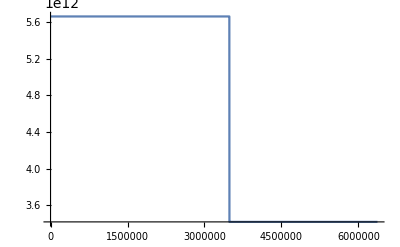

```mathematica
GetCaptureRate["mpD"/.mpDPoints[[1]],("mpD"/.mpDPoints[[1]])("meD/mpD"/.meDPoints[[1]]),v0Points[[2]]]
```

## Scrap

#### Unit Test get trajectory

InterpolatingFunction::dmval: Input value {-27.7496,Log[20000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

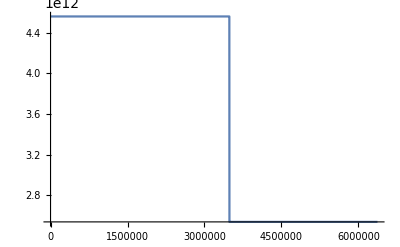

```mathematica
Plot[ELEarthTot[r,"mpD"/.mpDPoints[[1]],v0Points[[1]]]/.r->rt,{rt,1,"rE"/.Constants`EarthRepl}]
```

```mathematica
?ΔrAveragedTot0
```

5.51745×10^6

{l→InterpolatingFunction[…]}

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,IndexedElementEvaluate,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,ParameterAddress,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid,VectorEvaluate}

{{0.,551.745}}

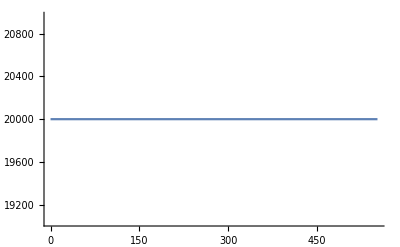

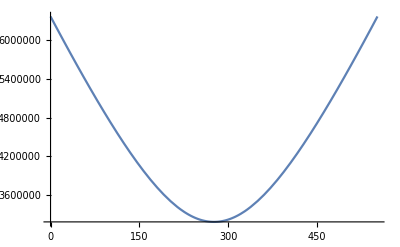

1.10349×10^7

```mathematica
REt=dE[(("rE")/2/.Constants`EarthRepl)]/2
s=NDSolve[{D[l[t],{t,2}]==0,l'[0]==v0Points[[1]],l[0]==-REt,WhenEvent[l[t]==REt,"StopIntegration"]},l,{t,0,10^4}][[1]]
(l/.s)["Methods"]
(l/.s)["Domain"]
Plot[l'[t]/.s,{t,0,%[[1,2]]}]

Plot[√((("rE")/2/.Constants`EarthRepl)^2+(l[t])^2)/.s,{t,0,%%[[1,2]]}]
```

5.51745×10^6

InterpolatingFunction::dmval: Input value {-27.7496,4.30103} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{l→InterpolatingFunction[…]}

{{0.,575.021}}

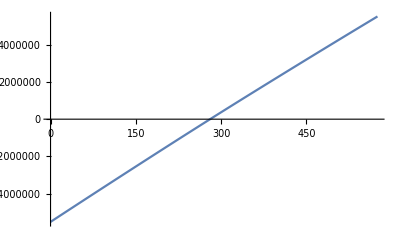

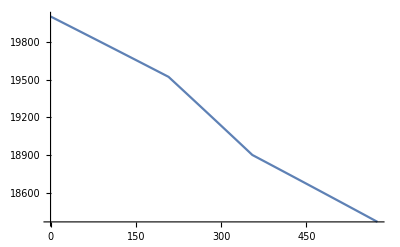

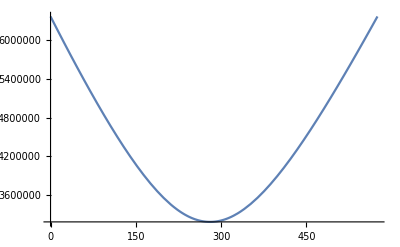

InterpolatingFunction::dmval: Input value {-27.7496,4.30103} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

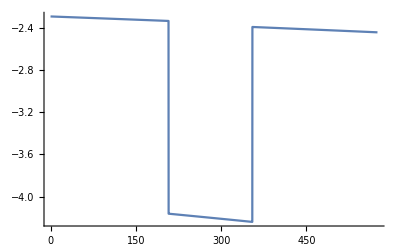

```mathematica
REt=dE[(("rE")/2/.Constants`EarthRepl)]/2
s=NDSolve[{D[l[t],{t,2}]==-((10^-10.5)^2("JpereV"/.Constants`SIConstRepl))/("mpD"/.mpDPoints[[1]])ELEarthTot[√((("rE")/2/.Constants`EarthRepl)^2+(l[t])^2),"mpD"/.mpDPoints[[1]],D[l[t],t]],l'[0]==v0Points[[1]],l[0]==-REt,WhenEvent[l[t]==REt,"StopIntegration"]},l,{t,0,10^4}][[1]]
ldom=(l/.s)["Domain"]
Plot[l[t]/.s,{t,0,ldom[[1,2]]}]
Plot[l'[t]/.s,{t,0,ldom[[1,2]]}]
Plot[√((("rE")/2/.Constants`EarthRepl)^2+(l[t])^2)/.s,{t,0,ldom[[1,2]]}]
Plot[-((10^-10.5)^2("JpereV"/.Constants`SIConstRepl))/("mpD"/.mpDPoints[[1]])ELEarthTot[√((("rE")/2/.Constants`EarthRepl)^2+(l[t]/.s)^2),"mpD"/.mpDPoints[[1]],Abs[(l'[t]/.s)]],{t,0,ldom[[1,2]]}]
```

```mathematica
(l/.s)[]
```

-5.571×10^6

```mathematica
-((10^-9)^2"JpereV"/.SIConstRepl)/("mpD"/.mpDPoints[[1]])ELEarthTot[√((("rE")/2/.Constants`EarthRepl)^2),"mpD"/.mpDPoints[[1]],Abs[20000]]
```

InterpolatingFunction::dmval: Input value {-27.7496,Log[20000]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

-4104.53

```mathematica
"rE"-"rcore"/.EarthRepl
```

2.885×10^6

```mathematica
√((("rE")/2/.Constants`EarthRepl)^2+(600000)^2)
```

3.24151×10^6

#### Unit Test Get weak capture probability

```mathematica
lDict=GetWeakCaptureTrajectory["mpD"/.mpDPoints[[1]],v0Points[[1]],(("rE")/2/.Constants`EarthRepl),10^-10.5]
```

InterpolatingFunction::dmval: Input value {-27.7496,4.30103} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

<|l(t)→InterpolatingFunction[…],v(t)→InterpolatingFunction[…],domain→{0.,575.021},RE→1.10349×10^7,κ→3.16228×10^-11,bE→3.1855×10^6,mχ→1.78×10^-28|>

```mathematica
("l(t)"/.lDict)[400]
("v(t)"/.lDict)[400]
```

2.26501×10^6

18794.

```mathematica
("dσf"/.FeσDictemep1GeV[[2]])[4,]
```

InterpolatingFunction[…][4]

```mathematica
"ωmin"/.FeσDictemep1GeV[[2]]
ξofωandvχ[10%,%,("v(t)"/.lDict)[t],"mpD"/.mpDPoints[[1]],SIConstRepl]/.t->300
Re@("dσf"/.FeσDictemep1GeV[[2]])[Log10[("v(t)"/.lDict)[t]],Log10@ξofωandvχ[10%%,%%,("v(t)"/.lDict)[t],"mpD"/.mpDPoints[[1]],SIConstRepl]]/.t->300
```

6.5887×10^12

0.196182

-1.43955

```mathematica
"ξ"/.FeσDictemep1GeV[[2]]
```

{-4,-Log[10000/9999]/Log[10]}

```mathematica
Integrate["dσf"/.FeσDictemep1GeV[[2]] ]
```

```mathematica
lDict
```

<|l(t)→InterpolatingFunction[…],v(t)→InterpolatingFunction[…],domain→{0.,575.021},RE→1.10349×10^7,κ→3.16228×10^-11,bE→3.1855×10^6,mχ→1.78×10^-28|>

```mathematica
(10^("ξ")/.FeσDictemep1GeV[[2]])[[1]]
```

1/10000

```mathematica
GetWeakCaptureProbability[lDict,FeσDictemep1GeV[[2]]]
```

<|SurvivalProb→1.,CaptureProb→1.26121×10^-13|>

```mathematica
GetWeakCaptureProbability[lDict,FeσDictemep1GeV[[2]]]
```

<|SurvivalProb→1.,CaptureProb→1.26121×10^-13|>

```mathematica
Round[527.0012234]
```

527

```mathematica
(*FrontEndTokenExecute@"Save"*)
```

```mathematica
Abs[{0,1} -ϵ]
```

{Abs[ϵ],Abs[1-ϵ]}